## First Order Phase Transition Case 4.3 Complex Scalar in SU(2)xU(1) + Higgs

```mathematica
starttime=SessionTime[];
m=.
T=.
λ=.
dmu=.
f=.
Bmu=.
W0=.
mp=.
L1=.
x=.
μ=.
v=.


"H:";
H={Gp,(v+h+I*G0)*1/Sqrt[2]}(***);
Hmod[v_,h_,Gp_,G0_,Wp_,Z_,A_]=Sqrt[ComplexExpand[H.Conjugate[H],Gp,TargetFunctions->Conjugate]];
"ϕ:";
phi[ρ_,η_]=η+I*ρ;
"ϕ^*:";
phistar[ρ_,η_]=ComplexExpand[Conjugate[phi[ρ,η]]];

(*x=ArcSin[0.1];*)

"Diagonalising η and ρ:";
(*η=rotmatin[[2,1]]OverTilde[ρ] + rotmatin[[2,2]]OverTilde[η]
ρ=rotmatin[[1,1]]OverTilde[ρ] + rotmatin[[1,2]]OverTilde[η]*)
(*η=Sin[x]rhop + Cos[x]etap
ρ=Cos[x]rhop -Sin[x]etap*)


"∂_μ :";
Dmu=({{dmu,0},{0,dmu}}+I*g/2*{{W0,Sqrt[2]*Wp},{Sqrt[2]*Conjugate[Wp],-W0}}+I*g1/2*{{Bmu,0},{0,Bmu}});(**1/Sqrt[2]*) (*this was an extra 1/Sqrt[2] factor, mistaken when reading the notes*)

"Diagonalising B_μ and (W^0)_μ:";
Subscript[θ, w]=ArcSin[Sqrt[0.22336]];
Sin[Subscript[θ, w]];

Bmu = Cos[Subscript[θ, w]]*A-Sin[Subscript[θ, w]]*Z;
W0=Sin[Subscript[θ, w]]*A+Cos[Subscript[θ, w]]*Z;

"|DH|:";
DH=Dmu.H;
Kterm[v_,h_,Gp_,G0_,Wp_,Z_,A_]=Chop[Sqrt[ComplexExpand[DH.Conjugate[DH],{Gp,Wp},TargetFunctions->Conjugate]]];

"Lagrangian:";
ℒ[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]:=Chop[Kterm[v,h,Gp,G0,Wp,Z,A]^2+-1/2*m^2*Hmod[v,h,Gp,G0,Wp,Z,A]^2+1/4*λ*Hmod[v,h,Gp,G0,Wp,Z,A]^4+f*Hmod[v,h,Gp,G0,Wp,Z,A]*ψ*OverBar[ψ]+L1*Hmod[v,h,Gp,G0,Wp,Z,A]^2*phi[ρ,η]*phistar[ρ,η]+μ*Hmod[v,h,Gp,G0,Wp,Z,A]^2*(phi[ρ,η]+phistar[ρ,η])+mp^2*phi[ρ,η]*phistar[ρ,η]];

"Since differential operator does not contribute, momentarily setting δ=0:";
(*∂=0*)
dmu=0;

ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η];

"Field dependent masses:";
"M_vev:";
Mv[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],v],v]];
Subscript[M, vev][v_]=Chop[Mv[v,0,0,0,0,0,0,0,0,0]];

"M_h:"
Mh[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],h],h]];
Subscript[M, h][v_]=Chop[Mh[v,0,0,0,0,0,0,0,0,0]]


"M_(G^±):";
Mgpm[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],Gp],Conjugate[Gp]]];
Subscript[M, gpm][v_]=Chop[Mgpm[v,0,0,0,0,0,0,0,0,0]];

"M_(G^0):";
Mg0[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],G0],G0]];
Subscript[M, g0][v_]=Chop[Mg0[v,0,0,0,0,0,0,0,0,0]];

"M_(W^±):";
Mwpm[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],Wp],Conjugate[Wp]]];
Subscript[M, wpm][v_]=Chop[Mwpm[v,0,0,0,0,0,0,0,0,0]];

"M_(W^0):";
Mz[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],Z],Z]];
Subscript[M, Z][v_]=Chop[Mz[v,0,0,0,0,0,0,0,0,0]];

"M_A_μ:";
Mamu[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],A],A]];
Subscript[M, A][v_]=Chop[Mamu[v,0,0,0,0,0,0,0,0,0]];

"M_ψ:";
Mpsi[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],ψ],OverBar[ψ]];
Subscript[M, psi][v_]=Mpsi[v,0,0,0,0,0,0,0,0,0];

"M_ρ:";
Mrho[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],ρ],ρ]];
Subscript[M, rho][v_]=Mrho[v,0,0,0,0,0,0,0,0,0];

"M_η:";
Meta[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],η],η]];
Subscript[M, eta][v_]=Meta[v,0,0,0,0,0,0,0,0,0];

"(∂^2/(∂h ∂η))^(1/2):";
M1[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],η],h]];
Subscript[M, 1][v_]=M1[v,0,0,0,0,0,0,0,0,0];

"(∂^2/(∂η ∂h))^(1/2):";
M2[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_,ρ_,η_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ,ρ,η],h],η]];
Subscript[M, 2][v_]=M2[v,0,0,0,0,0,0,0,0,0];

"Tree-level potential:"
Subscript[V, tree][v_]:=ℒ[v,0,0,0,0,0,0,0,0,0]
Subscript[V, tree][v];

"One-loop temperature independent corrections:"
Subscript[V, 1-loop][v_]:=1/(64*Pi^2)*(Subscript[n, vev]*(Subscript[M, vev][v])^4(Log[(Subscript[M, vev][v])^2/Q^2]-c)+Subscript[n, gpm]*(Subscript[M, gpm][v])^4(Log[(Subscript[M, gpm][v])^2/Q^2]-cb)+Subscript[n, g0]*(Subscript[M, g0][v])^4(Log[(Subscript[M, g0][v])^2/Q^2]-cb)+Subscript[n, w0]*(Subscript[M, Z][v])^4(Log[(Subscript[M, Z][v])^2/Q^2]-cb)+Subscript[n, wpm]*(Subscript[M, wpm][v])^4(Log[(Subscript[M, wpm][v])^2/Q^2]-cb)+Subscript[n, psi]*(Subscript[M, psi][v])^4(Log[(Subscript[M, psi][v])^2/Q^2]-c)+Subscript[n, eta]*(Subscript[M, eta][v])^4(Log[(Subscript[M, eta][v])^2/Q^2]-cb)+Subscript[n, rho]*(Subscript[M, rho][v])^4(Log[(Subscript[M, rho][v])^2/Q^2]-cb))
Subscript[V, 1-loop][v];

"High Temperature Expansion:"
Subscript[V, Temp][v_]:=1/(2*Pi^2)*(Subscript[n, vev]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, vev][v])^2-Pi/6*T*(Subscript[M, vev][v])^3)+Subscript[n, gpm]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, gpm][v])^2-Pi/6*T*(Subscript[M, gpm][v])^3)+Subscript[n, g0]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, g0][v])^2-Pi/6*T*(Subscript[M, g0][v])^3)+Subscript[n, w0]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, Z][v])^2-Pi/6*T*(Subscript[M, Z][v])^3)+Subscript[n, wpm]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, wpm][v])^2-Pi/6*T*(Subscript[M, wpm][v])^3)+Subscript[n, a]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, A][v])^2-Pi/6*T*(Subscript[M, A][v])^3)+Subscript[n, psi]((7*Pi^4*T^4)/360-Pi^2/24*T^2(Subscript[M, psi][v])^2)+Subscript[n, eta]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, eta][v])^2-Pi/6*T*(Subscript[M, eta][v])^3)+Subscript[n, rho]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, rho][v])^2-Pi/6*T*(Subscript[M, rho][v])^3))
Subscript[V, Temp][v];

"Effective potential:"
Subscript[V, total][v_]:=Subscript[V, tree][v]+Subscript[V, 1-loop][v]+Subscript[V, Temp][v]
Subscript[V, total][v];

"Physical parameters:";
(*λ=lam;*)
mhiggs=125;
mtop=172; (*GeV*)
f=mtop*Sqrt[2]/Q*1.;(*Yukawa coupling*)
(*m=mvev;(*93*)*)
(*λ=(m/Q)^2;*)(*0.54375 came from the expresion vev=m/Sqrt[λ]*)
Subscript[n, vev]=1;
Subscript[n, a]=2;
Subscript[n, g0]=1;
Subscript[n, gpm]=2;
Subscript[n, w0]=3;
Subscript[n, wpm]=6;
Subscript[n, psi]=-4;
Subscript[n, eta]=1;
Subscript[n, rho]=1;
(* retrived from http://www.damtp.cam.ac.uk/user/tong/qft/six.pdf*)
c=3/2;
cb=1/2;
Q=246;
e=0.303;
g=(e*1.)/Sin[Subscript[θ, w]];
g1=g*Tan[Subscript[θ, w]];
T=.(*critical temperature = 181.1221008747816*);
dT=10;

"Plotting parameters:";
min = 0;
max = 250;
step = 1;

(*V0[k_]=Subscript[V, total][k]*)

L1var=0.1;

"Matrix of effective masses:";
matrix=Chop[{{(Subscript[M, eta][v])^2,1/2(Subscript[M, 1][v])^2},{1/2(Subscript[M, 2][v])^2,(Subscript[M, h][v])^2}}];

matrix//MatrixForm

"Diagonalising the matrix:";
{{em1,em2},{ev1,ev2}} = Eigensystem[matrix];
"Eigenvalues:";
{em1,em2}=FullSimplify[{em1,em2}];

"Normalised Eigenvectors:";
ev1norm=1/Sqrt[ev1.ev1]*ev1;(*/.v->Q/.m->mvev/.λ->lam/.L1->L1var;*)
ev2norm=1/Sqrt[ev2.ev2]*ev2;(*/.v->Q/.m->mvev/.λ->lam/.L1->L1var;*)
f1={h,η};
etap=ev2norm*f1;
hp=ev1norm*f1;
f2={hp,etap};
f2//MatrixForm;

eigenm={{ev1norm[[1]],ev2norm[[1]]},{ev1norm[[2]],ev2norm[[2]]}};
rot={{Cos[x],-Sin[x]},{Sin[x],Cos[x]}};
diag1=FullSimplify[Inverse[eigenm].matrix.eigenm];
diag2=FullSimplify[Inverse[rot].matrix.rot];
diag1//MatrixForm
diag2//MatrixForm

"Condition 1: sin[x]==0.1"
sineterm=Sin[1/2 ArcTan[(v*μ)/(1/8*Sqrt[2 m^2+8 mp^2+v^2(4*L1-3λ)])]];
{{muexp}}=Solve[sineterm==0.1,μ]

"Condition 2: eigenvalue must equal higgs mass:"
(*mpexp=Solve[(em1/.mu1)==125^2,mp]*)
{{mp1},{mp2}}=Solve[(em1/.muexp)==125^2,mp];

{{l1},{l2},{l3}}=Solve[(em2/.muexp/.mp1)==50^2,λ];
(*only l3 is real, l1 l2 are complex*)

(*"Zeroth value:"
d=Limit[(Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.m->101.375),v->0]*)

"Now that μ,mp and λ have been elimnated. Substitute expresison into V_total:" 
"(∂SubscriptBox[V, total])/(∂v):"
(*Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var;*)

"Parameter fixing:"
"m:"
m=.;(*for 150^2,m=101.375*)
dm=0.1;
Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var
"Zeroth value:"
d=Limit[(Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var),v->0]
(*"data:"
data=Table[1.*Re[Limit[Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var,v->j]-d],{j,min,max,step}];(*min starts at 1 because we already know at h=0 the value is zero because of V0[k->0]*)
(*"Plot:"
ListPlot[data,Joined->True,AxesLabel->{v,V[v]},DataRange->{0,max}]*)

minval=Min[data]
pos = Position[data,minval]
"Vev value:"
(pos[[1,1]]-1)*step*1

If[m>250,Print[Did not work],While[Abs[(pos[[1,1]]-1)*step-Q]>0.1,If[(pos[[1,1]]-1)>Q,Print[{{"dm",dm=dm/2},{"m",m = 1.*(m-dm)}, {"Min",data=Table[1.*Re[Limit[Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var,v->j]-d],{j,min,max,step}];,minval = Min[data]},{"vev",pos=Position[data,minval];,(pos[[1,1]]-1)*step}}],If[(pos[[1,1]]-1)<Q,Print[{{"dm",dm=dm},{"m",m = 1.*(m+dm)}, {"Min",data=Table[1.*Re[Limit[Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var,v->j]-d],{j,min,max,step}];,minval = Min[data]},{"vev",pos=Position[data,minval];,(pos[[1,1]]-1)*step}}]]]]]
"Fixed m:"
m

"Loop begins"
"{dT,T,min,v}"
(*only subtract by dT if minval>0 since at low temperatures, the minimum is always below negative*)

threshold = 0.01; (*the criteria in which the While loop will cease*)
ϵ=Length[data]*0.95; (* interval for finding minimum *)
"Vexp:"
Vexp[v_]=Subscript[V, total][v]/.muexp/.mp1/.l3/.L1->L1var;
"Zeroth value:"
V0[k_]=Vexp[v]/.v->k;

"Seed T here:";
T=0;(*for 150^2, T=57.52948999404907*);
(*only temporarily here to check plot*)
"Zeroth value:"
d=Limit[(Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var),v->0]
"data:"
data=Table[1.*Re[Limit[Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var,v->j]-d],{j,min,max,step}];

"Plot:"
ListPlot[data,Joined->True,AxesLabel->{"v/GeV","V(v)/GeV^4"},DataRange->{0,max}]

minval=Min[data]
pos = Position[data,minval]
"Vev value at zero T:"
vc=(pos[[1,1]]-1)*step*1

If[T>1000,Print["Second Order Phase Transition"],While[Abs[minval] > threshold,If[minval>0,Print[{{"dT",dT = dT/2}, {"T",T = 1.*(T-dT)}, {"Min",data=Table[1.*(Re[Limit[Vexp[v]/.T->T,v->j]-Limit[V0[k],k->0]]),{j,min,vc*1.5,step}];,minval = Min[Take[data,-Ceiling[ϵ]]]},{"v",pos=Position[data,minval];,pos[[1,1]]*step}}],If[minval <0, Print[{{"dT",dT},{"T",T = 1.*(T+dT)}, {"Min",data=Table[1.*(Re[Limit[Vexp[v],v->j]-Limit[V0[k],k->0]]),{j,min,vc*1.5,step}];,minval = Min[Take[data,-Ceiling[ϵ]]]},{"v",pos=Position[data,minval];,pos[[1,1]]*step}}]]]]]
(*Min[Take[data,{Ceiling[pos[[1,1]]*step-ϵ],Ceiling[pos[[1,1]]*step+ϵ]}]]*)

"Loop completed"

"Critical temperature, T_c:"
T*1.

"New min:"
minval*1.

"ϕ value:"
vc=(pos[[1,1]]-1)*step
data;

"Strength:"
vc/T*1.


img1=ListPlot[Table[1.*(Limit[Vexp[v],v->j]-Limit[V0[k],k->0]),{j,0,vc*1.5,step}],Joined->True,AxesLabel->{v,V[v]},DataRange->{0,vc*1.5}]

"Whole plot:"
img2=ListPlot[Table[1.*(Limit[Vexp[v],v->j]-Limit[V0[k],k->0]),{j,-vc*1.5,vc*1.5,step}],Joined->True,AxesLabel->{v,V[v]},DataRange->{-vc*1.5,vc*1.5}]

(*m=101(*my estimation*)*)
"λ:"
λ=λ/.l3/.L1->L1var/.v->246


"mp:"
mp/.mp1/.L1->L1var(*/.v->246*)
"μ:"
μ/.muexp/.mp1/.L1->L1var(*/.v->246*)

"Sin term:"
sineterm/.T->0/.muexp/.mp1/.l3/.L1->L1var/.v->246
"Final Eigenvalues:"
"Eigenvalue 1:"
Sqrt[em1]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.v->246
"Eigenvalue 2:"
Sqrt[em2]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.v->246

Sqrt[diag1]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.v->246//MatrixForm

(*Subscript[V, total][v]/.L1->L1var*)
"Zeroth value:"
(*d=Limit[(Subscript[V, total][v]/.T->0/.L1->L1var),v->0]*)
(*d=Limit[(Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.m->101.375),v->0]
"data:"
data=Table[1.*(Re[Limit[(Subscript[V, total][v]/.T->0/.muexp/.mp1/.l3/.L1->L1var/.m->101.375),v->j]-d]),{j,min,max,step}];(*min starts at 1 because we already know at h=0 the value is zero because of V0[k->0]*)
"Plot:"
ListPlot[data,Joined->True,AxesLabel->{v,V[v]},DataRange->{0,max}]*)*)

"Total computation time (s):"
endtime=SessionTime[];
endtime-starttime
```

M_h:

√(-m^2/2+(3 v^2 λ)/4)

Tree-level potential:

One-loop temperature independent corrections:

High Temperature Expansion:

Effective potential:

(2 mp^2+L1 v^2 | v μ
v μ | -m^2/2+(3 v^2 λ)/4)

(1/8 (-2 m^2+8 mp^2+v^2 (4 L1+3 λ)-√((2 m^2+8 mp^2+v^2 (4 L1-3 λ))^2+64 v^2 μ^2)) | 0
0 | 1/8 (-2 m^2+8 mp^2+v^2 (4 L1+3 λ)+√((2 m^2+8 mp^2+v^2 (4 L1-3 λ))^2+64 v^2 μ^2)))

((2 mp^2+L1 v^2) Cos[x]^2+1/4 (-2 m^2+3 v^2 λ) Sin[x]^2+v μ Sin[2 x] | v μ Cos[2 x]-1/8 (2 m^2+8 mp^2+v^2 (4 L1-3 λ)) Sin[2 x]
v μ Cos[2 x]-1/8 (2 m^2+8 mp^2+v^2 (4 L1-3 λ)) Sin[2 x] | 1/4 (-2 m^2+3 v^2 λ) Cos[x]^2-2 v μ Cos[x] Sin[x]+(2 mp^2+L1 v^2) Sin[x]^2)

Condition 1: sin[x]==0.1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→(0.0253823 √(2. m^2+8. mp^2+4. L1 v^2-3. v^2 λ))/v}}

Condition 2: eigenvalue must equal higgs mass:

Now that μ,mp and λ have been elimnated. Substitute expresison into V_total:

(∂SubscriptBox[V, total])/(∂v):

Parameter fixing:

m:

-1/4 m^2 v^2+(0.+9 (0.+0. (v^2)^(3/2)))/(2 π^2)+1/16 v^4 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/(64 π^2)(0.0633565 v^4 (-1/2+Log[1.69805×10^-6 v^2])+0.0525196 v^4 (-1/2+Log[2.1864×10^-6 v^2])-0.955946 v^4 (-3/2+Log[8.07823×10^-6 v^2])+3 (-m^2/2+1/4 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3)))^2 (-1/2+Log[1/60516(-m^2/2+1/4 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3)))])+(-m^2/2+3/4 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3)))^2 (-3/2+Log[1/60516(-m^2/2+3/4 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3)))])+2 ((0.1 v^2+(2. (3.75156×10^13+1.2005×10^9 m^2-2.401×10^8 v^2-7683.2 m^2 v^2-1.80075×10^9 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+11524.8 v^4 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))))/(4.802×10^9+153664. m^2-230496. v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3)))))^2 (-1/2+Log[1/60516(0.1 v^2+(2. (3.75156×10^13+1.2005×10^9 m^2-2.401×10^8 v^2-7683.2 m^2 v^2-1.80075×10^9 v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+11524.8 v^4 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))))/(4.802×10^9+153664. m^2-230496. v^2 (-(1.54696×10^-57 (-9.69643×10^60-4.30953×10^56 m^2))/v^2-(1.94905×10^-57 (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10))/(v^6 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))+1/v^6 1.22782×10^-57 (-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14+√(4. (-1.42192×10^121 v^8+1.95956×10^102 m^2 v^8-2.99705×10^72 m^4 v^8+7.49699×10^100 v^10)^3+(-1.07236×10^182 v^12-3.15949×10^163 m^2 v^12-2.02295×10^159 m^4 v^12+1.0377×10^109 m^6 v^12-9.89803×10^161 v^14-9.69255×10^157 m^2 v^14)^2))^(1/3))))]))

Zeroth value:

0.00158314 ((2. (-9.98116×10^73+1.37551×10^55 m^2-2.10378×10^25 m^4+2.10087×10^13 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)-4.42201×10^-48 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(2/3))^2 (-0.5+Log[(0.0000165246 (-9.98116×10^73+1.37551×10^55 m^2-2.10378×10^25 m^4+2.10087×10^13 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)-4.42201×10^-48 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(2/3)))/(-6.38794×10^69+8.80329×10^50 m^2-1.34642×10^21 m^4+1.34456×10^9 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)-2.83008×10^-52 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(2/3))]))/(-6.38794×10^69+8.80329×10^50 m^2-1.34642×10^21 m^4+1.34456×10^9 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)-2.83008×10^-52 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(2/3))^2+3. (-0.5 m^2+0.25 (15000.+0.666667 m^2+(2.77139×10^64-3.81928×10^45 m^2+5.84139×10^15 m^4)/(-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)+1.22782×10^-57 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)))^2 (-0.5+Log[0.0000165246 (-0.5 m^2+0.25 (15000.+0.666667 m^2+(2.77139×10^64-3.81928×10^45 m^2+5.84139×10^15 m^4)/(-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)+1.22782×10^-57 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)))])+(-0.5 m^2+0.75 (15000.+0.666667 m^2+(2.77139×10^64-3.81928×10^45 m^2+5.84139×10^15 m^4)/(-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)+1.22782×10^-57 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)))^2 (-1.5+Log[0.0000165246 (-0.5 m^2+0.75 (15000.+0.666667 m^2+(2.77139×10^64-3.81928×10^45 m^2+5.84139×10^15 m^4)/(-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)+1.22782×10^-57 (-1.07236×10^182-3.15949×10^163 m^2-2.02295×10^159 m^4+1.0377×10^109 m^6+√(8.42470637416474×10^349+1.15305998685189×10^346 m^2+4.33868003388094×10^341 m^4+1.27829919739688×10^323 m^6+4.09232575444625×10^318 m^8-4.19841×10^268 m^10))^(1/3)))]))

Total computation time (s):

19.65713

```mathematica
Manipulate[ListPlot[Table[Re[-1/4 m^2 v^2+(0.+9 (0.+0. (v^2)^(3/2)))/(2 π^2)+1/16 v^4 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/(64 π^2)(0.06335647116102723 v^4 (-1/2+Log[1.6980467797855348*^-6 v^2])+0.05251960787605467 v^4 (-1/2+Log[2.1864013954799323*^-6 v^2])-0.9559459785160639 v^4 (-3/2+Log[8.078234675128986*^-6 v^2])+3 (-m^2/2+1/4 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3)))^2 (-1/2+Log[1/60516(-m^2/2+1/4 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3)))])+(-m^2/2+3/4 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3)))^2 (-3/2+Log[1/60516(-m^2/2+3/4 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3)))])+2 ((0.1 v^2+(2. (3.7515625*^13+1.200499802*^9 m^2-2.4010003960000002*^8 v^2-7683.200000000001 m^2 v^2-1.800749703*^9 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+11524.800000000001 v^4 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))))/(4.802000792*^9+153664. m^2-230496. v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3)))))^2 (-1/2+Log[1/60516(0.1 v^2+(2. (3.7515625*^13+1.200499802*^9 m^2-2.4010003960000002*^8 v^2-7683.200000000001 m^2 v^2-1.800749703*^9 v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+11524.800000000001 v^4 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))))/(4.802000792*^9+153664. m^2-230496. v^2 (-(1.5469607073322318*^-57 (-9.696434670235513*^60-4.3095255329163996*^56 m^2))/v^2-(1.949048358528141*^-57 (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10))/(v^6 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))+1/v^6 1.2278235270863273*^-57 (-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14+√(4. (-1.4219195400377574*^121 v^8+1.9595623948037164*^102 m^2 v^8-2.9970460840885117*^72 m^4 v^8+7.496994389471782*^100 v^10)^3+(-1.0723647486205205*^182 v^12-3.159493179431672*^163 m^2 v^12-2.022949765675423*^159 m^4 v^12+1.0376959627017534*^109 m^6 v^12-9.898033606502046*^161 v^14-9.692546622467892*^157 m^2 v^14)^2))^(1/3))))]))-(0.0015831434944115277 ((2. (-9.981159242403426*^73+1.3755141382642473*^55 m^2-2.103775451409488*^25 m^4+2.1008746535002043*^13 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)-4.422005703474233*^-48 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(2/3))^2 (-0.5+Log[(0.000016524555489457333 (-9.981159242403426*^73+1.3755141382642473*^55 m^2-2.103775451409488*^25 m^4+2.1008746535002043*^13 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)-4.422005703474233*^-48 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(2/3)))/(-6.387942968709794*^69+8.803291936829377*^50 m^2-1.3464165109682688*^21 m^4+1.34456*^9 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)-2.830084116992901*^-52 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(2/3))]))/(-6.387942968709794*^69+8.803291936829377*^50 m^2-1.3464165109682688*^21 m^4+1.34456*^9 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)-2.830084116992901*^-52 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(2/3))^2+3. (-0.5 m^2+0.25 (15000.003436068304+0.6666666666666666 m^2+(2.7713899454696806*^64-3.819281869025657*^45 m^2+5.841387750625907*^15 m^4)/(-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)+1.2278235270863273*^-57 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)))^2 (-0.5+Log[0.000016524555489457333 (-0.5 m^2+0.25 (15000.003436068304+0.6666666666666666 m^2+(2.7713899454696806*^64-3.819281869025657*^45 m^2+5.841387750625907*^15 m^4)/(-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)+1.2278235270863273*^-57 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)))])+(-0.5 m^2+0.75 (15000.003436068304+0.6666666666666666 m^2+(2.7713899454696806*^64-3.819281869025657*^45 m^2+5.841387750625907*^15 m^4)/(-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)+1.2278235270863273*^-57 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)))^2 (-1.5+Log[0.000016524555489457333 (-0.5 m^2+0.75 (15000.003436068304+0.6666666666666666 m^2+(2.7713899454696806*^64-3.819281869025657*^45 m^2+5.841387750625907*^15 m^4)/(-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)+1.2278235270863273*^-57 (-1.0723647486205205*^182-3.159493179431672*^163 m^2-2.022949765675423*^159 m^4+1.0376959627017534*^109 m^6+√(8.4247063741647449209136942397286543753345`15.954589770191005*^349+1.15305998685188522128095061212988178817`15.50362547286886*^346 m^2+4.3386800338809353368954831246772972344229987975189272`15.653559774527023*^341 m^4+1.27829919739688004561923621417127184835445716181008103`15.653559774527091*^323 m^6+4.092325754446248965279765890870729013145614807096`15.653559774527023*^318 m^8-4.1984136091796894*^268 m^10))^(1/3)))])))],{v,min,max,step}],Joined->True,DataRange->{0,max}],{m,0,400,0.1}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Q
```

246

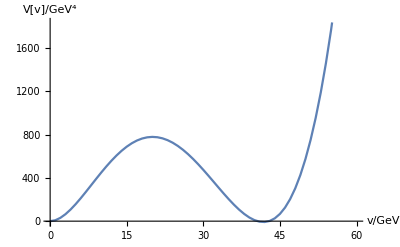

```mathematica
ListPlot[data,Joined->True,AxesLabel->{"v/GeV","V[v]/GeV^4"},DataRange->{0,60}]
```